```mathematica
Fourier[allvertices][[1]]
```

{-1.32432×10^-12-1.23307×10^-15 ⅈ,3.10734×10^-12-4.31575×10^-15 ⅈ}

```mathematica
FOUTpts=StringJoin["2D_PA_","F2_F1_",ToString[F2],"_",ToString[F1],"__N",ToString[numlines+1],"_Len",ToString[Length[pts]],"_pts.txt"];
FOUTuniq=StringJoin["2D_PA_","F2_F1_",ToString[F2],"_",ToString[F1],"__N",ToString[numlines+1],"_Len",ToString[Length[UniqueGridVertices]],"_uniq.txt"];
FOUTtiles=StringJoin["2D_PA_","F2_F1_",ToString[F2],"_",ToString[F1],"__N",ToString[numlines+1],"_Len",ToString[Length[tiles2]],"_tiles.txt"];
FOUTtilesimg=StringJoin["2D_PA_","F2_F1_",ToString[F2],"_",ToString[F1],"__N",ToString[numlines+1],"_Len",ToString[Length[tiles2]],"_tiles.bmp"]
Export[FOUTpts,pts,"Table"]
Export[FOUTuniq,UniqueGridVertices,"Table"]
Export[FOUTtiles,tiles2,"Table"]
Export[FOUTtilesimg,g]
```

2D_PA_F2_F1_5_3__N21_Len1579_tiles.bmp

2D_PA_F2_F1_5_3__N21_Len1579_pts.txt

2D_PA_F2_F1_5_3__N21_Len1579_uniq.txt

2D_PA_F2_F1_5_3__N21_Len1579_tiles.txt

2D_PA_F2_F1_5_3__N21_Len1579_tiles.bmp

```mathematica
tmpp=pts[[Flatten[Position[pts[[All,3]],_?(Abs[#[[1]]]<maxlength&&Abs[#[[2]]]<maxlength&&Abs[#[[3]]]<maxlength&)]]]]
```

Part::partd: Part specification List ⟦ 1 ⟧ is longer than depth of object.

Part::partd: Part specification List ⟦ 2 ⟧ is longer than depth of object.

Part::partd: Part specification List ⟦ 3 ⟧ is longer than depth of object.

General::stop: Further output of Part :: partd will be suppressed during this calculation.

{{{10,16},{1,4},{-0.99,-7.10986,0}},{{19,16},{4,5},{-4.70703,-7.09772,0}},{{7,3},{1,2},{-3.99,-7.09424,0}},1573,{{7,3},{1,5},{-3.99,7.06076,0}},{{17,2},{1,4},{6.01,7.07369,0}},{{10,3},{4,5},{-3.89508,7.09645,0}}}
 |  |  |  |

```mathematica
CountInstances[tmpp,tolerance]
```

```mathematica
Length[{{{{{10,16},{1,4},{-0.9899999999999998,-7.109863949919857,0},1},{{19,16},{4,5},{-4.707030638903822,-7.097715030807465,0},1},{{7,3},{1,2},{-3.99,-7.094238961452076,0},1},1573,{{7,3},{1,5},{-3.9900000000000007,7.060756241813828,0},1},{{17,2},{1,4},{6.009999999999999,7.073685240639047,0},1},{{10,3},{4,5},{-3.8950834546006736,7.096450094676929,0},1}}}, {{{, , , , }}}}]
```

1579

```mathematica
Length[tmpp]
```

1579

```mathematica
UniqueGridVertices[[Flatten[Position[UniqueGridVertices[[All,4]],_?(#>1&)]]]]
```

{{{6,11},{1,3},{-4.99,-8.87224,0},3},{{3,11},{2,3},{-3.99,-7.09424,0},3},{{8,11},{1,3},{-2.99,-5.31623,0},3},{{7,11},{2,3},{-1.99,-3.53823,0},3},{{10,11},{1,3},{-0.99,-1.76022,0},3},{{11,11},{1,2},{0.01,0.01778,0},3},{{12,13},{1,2},{1.01,1.79578,0},3},{{13,15},{1,2},{2.01,3.57379,0},3},{{14,17},{1,2},{3.01,5.35179,0},3},{{15,19},{1,2},{4.01,7.1298,0},3},{{16,21},{1,2},{5.01,8.9078,0},3}}

```mathematica
Flatten[Position[UniqueGridVertices[[All,1]],{11,11}]]
```

{2191,2192,2193,2194,2195,2196,2197,2198}

```mathematica
UniqueGridVertices[[2197]]
```

{{11,11},{1,2},{0.01,0.01778,0},3}

```mathematica
sing=tiles2[[Flatten[Position[tiles2[[All,3]],_?(Length[#]==3&)]]]][[All,1]];
```

FittedModel[-0.26906+1.72599 x]

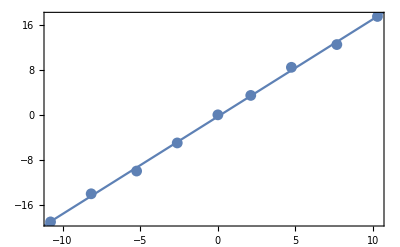

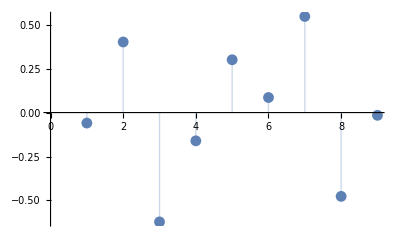

```mathematica
lm=LinearModelFit[sing,x,x]
Show[ListPlot[sing],Plot[lm[x],{x,-12,12}],Frame->True]
ListPlot[lm["FitResiduals"],Filling->Axis]
```

```mathematica
Length[Position[tiles2[[All,3]],_?(Length[#]==3&)]]
```

540

```mathematica
ShiftedSpacings//MatrixForm
```

(-4.99 | -3.99 | -2.99 | -1.99 | -0.99 | 0.01 | 1.01 | 2.01 | 3.01 | 4.01 | 5.01
-4.98 | -3.98 | -2.98 | -1.98 | -0.98 | 0.02 | 1.02 | 2.02 | 3.02 | 4.02 | 5.02
-4.99 | -3.99 | -2.99 | -1.99 | -0.99 | 0.01 | 1.01 | 2.01 | 3.01 | 4.01 | 5.01
-5.03 | -4.03 | -3.03 | -2.03 | -1.03 | -0.03 | 0.97 | 1.97 | 2.97 | 3.97 | 4.97
-5.01 | -4.01 | -3.01 | -2.01 | -1.01 | -0.01 | 0.99 | 1.99 | 2.99 | 3.99 | 4.99)

```mathematica
Table[v2[[{1,2}]].i,{i,starvectors[[All,{1,2}]]}]
tmp=testpt.starvectors[[1,{1,2}]]
Table[x-tmp,{x,ShiftedSpacings[[1]]}]
```

{-1.87041,4.02032,5.01096,-1.32872,-5.01096}

-1.86961

{-3.12039,-2.12039,-1.12039,-0.120392,0.879608,1.87961,2.87961,3.87961,4.87961,5.87961,6.87961}

```mathematica
ShiftedSpacings[[3,numlines+1]]
```

5.01

```mathematica
Abs[N[starvectors[[3]]]]
```

{0.587785,0.809017,0.}

```mathematica
Table[Table[Abs[spacing/Abs[starvectors[[i]]].{1,1,0}],{spacing,{ShiftedSpacings[[i,1]],ShiftedSpacings[[i,numlines+1]]}}],{i,Range[numvectors]}]
```

{{4.99,5.01},{3.95215,3.98389},{3.57245,3.58676},{3.60108,3.55813},{3.58676,3.57245}}

```mathematica
Position[ShiftedSpacings[[3]],_?(Chop[#-v2[[{1,2}]].starvectors[[3,{1,2}]]]≥0&)]
```

{}

{{11,11},{1,2},{0.01,0.01778,0},3}

{0.01,0.01778,0}

Part::partw: Part 2 of {{0.0102961, 0.0168249}} does not exist.

Part::partw: Part 3 of {{0.0102961, 0.0168249}} does not exist.

{11,11,11,11,11}

{12,11,11,11,12}

Dot::dotsh: Tensors {{{0.0102961, 0.0168249}} ⟦ 2 ⟧, 0} and {1, 0, 0} have incompatible shapes.

General::stop: Further output of Dot :: dotsh will be suppressed during this calculation.

{}

Dot::dotsh: Tensors {{{0.0102961, 0.0168249}} ⟦ 3 ⟧, 0} and {1, 0, 0} have incompatible shapes.

General::stop: Further output of Dot :: dotsh will be suppressed during this calculation.

{}

{0.01,0.01778}

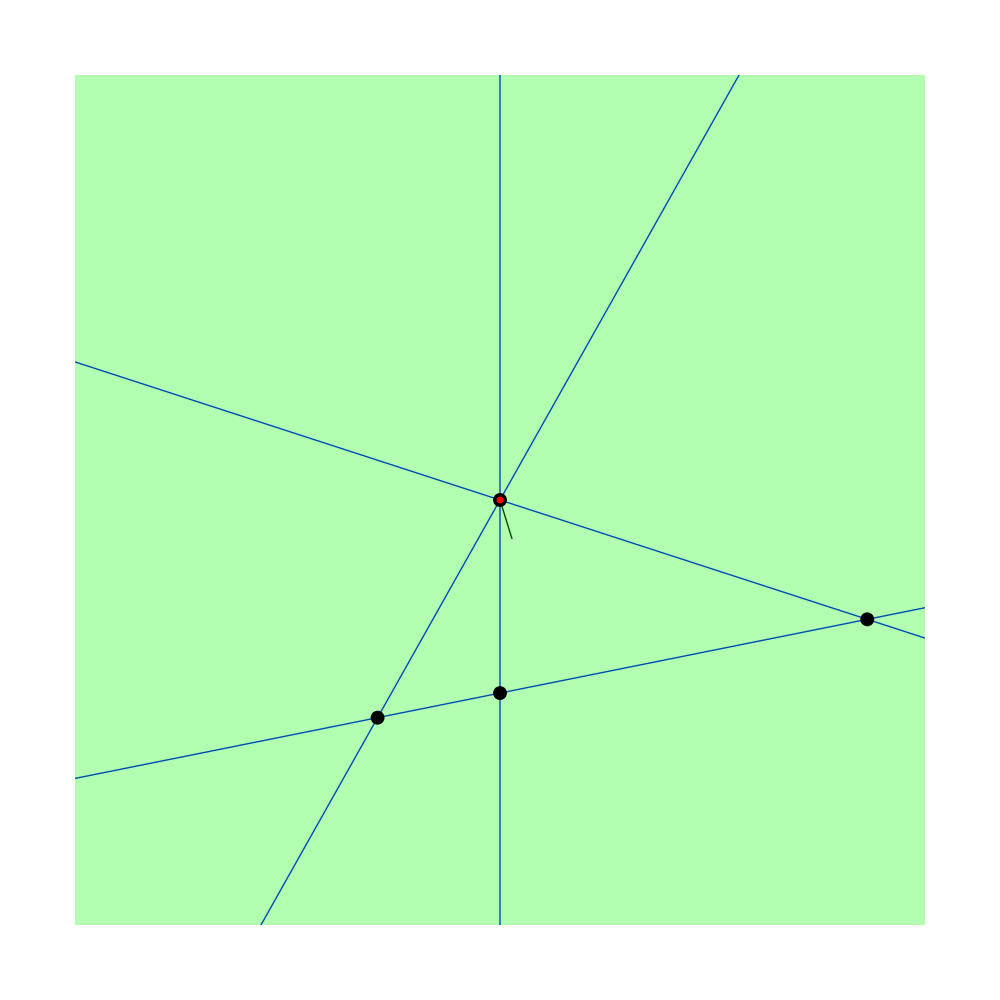

```mathematica
UniqueGridVertices[[2197]]
testpt=UniqueGridVertices[[2197,3]]

v1=Flatten[{ProbeVectors[[1]],0}];
v2=Flatten[{ProbeVectors[[2]],0}];
v3=Flatten[{ProbeVectors[[3]],0}];

FindGridIndices[testpt]
FindGridIndices[v1]
FindGridIndices[v2]
FindGridIndices[v3]

testpt=testpt[[{1,2}]]
eps=10^-4;
zoom=10^-3;
UpDown={-1,1};
ProbeIndices=Tuples[{UpDown,UpDown,UpDown,UpDown,UpDown}];
ProbeVectors=N[Table[testpt+eps*Normalize[n.starvectors][[{1,2}]],{n,ProbeIndices[[{2}]]}]];
ProbeVectorsArrow =Graphics[Line[{testpt,#}]&/@ProbeVectors];

Show[ProbeVectorsArrow,

Table[Plot[-starvectors[[i,1]]/starvectors[[i,2]]*x+ShiftedSpacings[[i,j]]/starvectors[[i,2]],{x,-maxlength,maxlength},PlotStyle->{Blue,Thin}],{i,Range[2,5]},{j,Range[numlines+1]}],
Table[Graphics[{Blue,Thin,Line[{{x,-maxlength},{x,maxlength}}]}],{x,ShiftedSpacings[[1]]}],


Graphics[{Green,Opacity[0.3],Polygon[{{-maxlength,-maxlength},{-maxlength,maxlength},{maxlength,maxlength},{maxlength,-maxlength},{-maxlength,-maxlength}}]}],
Graphics[{PointSize[0.01],Point[UniqueGridVertices[[All,3,{1,2}]]]}](*option here gets rid of indeterminate values*),
Graphics[{PointSize[0.005],Red,Point[testpt]}],
AspectRatio->1,PlotRange->{{testpt[[1]]-zoom,testpt[[1]]+zoom},{testpt[[2]]-zoom,testpt[[2]]+zoom}},
ImageSize->1000
]
```